# MEA Example Notebook

## Initialization

Set the current working directory to the notebook's directory, then load the MEA analysis library from the current directory:

```mathematica
SetDirectory[NotebookDirectory[]]; 
NotebookEvaluate[FileNameJoin[{Directory[],"MEA_Analysis_Library.nb"}]];
```

## Load Data

Load a few channels (H11 and M5) of analog data. We typically don' t want to load the whole file since it will be so large:

```mathematica
analogData=MEA120AnalogImport[FileNameJoin[{Directory[],"I9119_Sample_Data","2014-10-30_I9119_Stimulate_D3.h5"}],{"H11","M5"}];
```

Load the spike data. This is a comma seperated value file generated with the python mea tool. You can also load a directory of timestamp file data as is exported by MC_Rack spike detection (select one file per channel):

```mathematica
spikeData=MEASpikeImport[FileNameJoin[{Directory[],"I9119_Sample_Data","2014-10-30_I9119_Stimulate_D3.csv"}]];
```

## Analyze Data

Let’s see some stats on the bursting behavior of a channel:

```mathematica
BurstStatistics[spikeData["H11"]]
```

Mean Burst Length () | 8.5
Burst Rate (bursts/s) | 0.320323
Mean Intra-Burst Interval (s) | 0.0819033
Mean Inter-Burst Interval (s) | 2.73391

## Visualize Data

### Analog Data

Display some analog data. We use TimeSeriesWindowResample to reduce the number of points displayed to improve speed. The specification list is given as {tmin, tmax, numberSamplePoints}, in this case display data from 0s to 15s and show 1000 points:

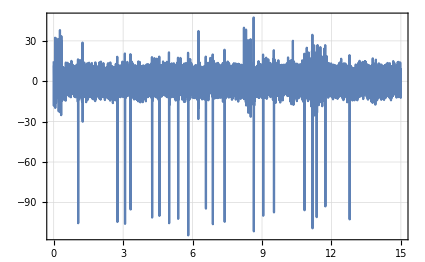

```mathematica
ListLinePlot[TimeSeriesWindowResample[analogData["M5"],{0,15,1000}]]
```

We can display both channels on the same graph, or on two graphs in a column:

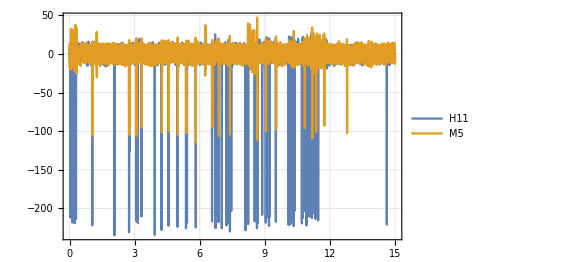

```mathematica
ListLinePlot[TimeSeriesWindowResample[analogData,{0,15,1000}],PlotLegends->Keys@analogData]
```

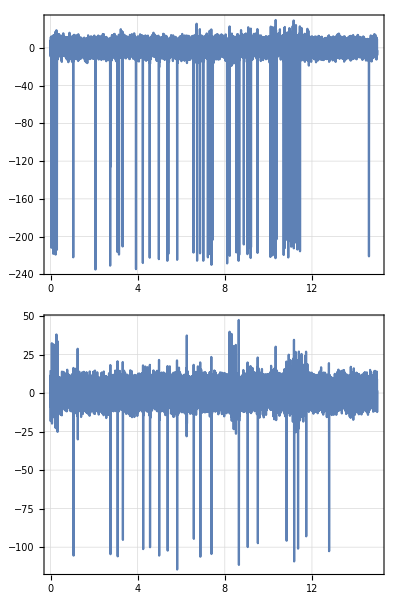

```mathematica
Column[ListLinePlot[TimeSeriesWindowResample[#,{0,15,1000}]]&/@Values[analogData]]
```

We can make it interactive too :

```mathematica
Manipulate[ListLinePlot[TimeSeriesWindowResample[analogData["H11"],{t,t+dt,1000}],PlotRange->{Automatic,{Min[analogData],30}}],{t,0,analogData["H11"]["LastTime"]},{{dt,1},0.05,10}]
```

ListLinePlot::prng: Value of option PlotRange -> {Automatic, {analogData, 30}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::lpn: TimeSeriesWindowResample[analogData["H11"], {0., 1., 1000.}] is not a list of numbers or pairs of numbers.

ListLinePlot::prng: Value of option PlotRange -> {Automatic, {analogData, 30}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::lpn: TimeSeriesWindowResample[analogData["H11"], {0., 1., 1000.}] is not a list of numbers or pairs of numbers.

ListLinePlot::prng: Value of option PlotRange -> {Automatic, {analogData, 30}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::lpn: TimeSeriesWindowResample[analogData["H11"], {0., 1., 1000.}] is not a list of numbers or pairs of numbers.

ListLinePlot::prng: Value of option PlotRange -> {Automatic, {analogData, 30}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::lpn: TimeSeriesWindowResample[analogData["H11"], {0., 1., 1000.}] is not a list of numbers or pairs of numbers.

ListLinePlot::prng: Value of option PlotRange -> {Automatic, {analogData, 30}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::lpn: TimeSeriesWindowResample[analogData["H11"], {0., 1., 1000.}] is not a list of numbers or pairs of numbers.

ListLinePlot::prng: Value of option PlotRange -> {Automatic, {analogData, 30}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::lpn: TimeSeriesWindowResample[analogData["H11"], {0., 1., 1000.}] is not a list of numbers or pairs of numbers.

ListLinePlot::prng: Value of option PlotRange -> {Automatic, {analogData, 30}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::lpn: TimeSeriesWindowResample[analogData["H11"], {0., 1., 1000.}] is not a list of numbers or pairs of numbers.

ListLinePlot::prng: Value of option PlotRange -> {Automatic, {analogData, 30}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::lpn: TimeSeriesWindowResample[analogData["H11"], {0., 1., 1000.}] is not a list of numbers or pairs of numbers.

ListLinePlot::prng: Value of option PlotRange -> {Automatic, {analogData, 30}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::lpn: TimeSeriesWindowResample[analogData["H11"], {0., 1., 1000.}] is not a list of numbers or pairs of numbers.

ListLinePlot::prng: Value of option PlotRange -> {Automatic, {analogData, 30}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::lpn: TimeSeriesWindowResample[analogData["H11"], {0., 1., 1000.}] is not a list of numbers or pairs of numbers.

ListLinePlot::prng: Value of option PlotRange -> {Automatic, {analogData, 30}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::lpn: TimeSeriesWindowResample[analogData["H11"], {0., 1., 1000.}] is not a list of numbers or pairs of numbers.

ListLinePlot::prng: Value of option PlotRange -> {Automatic, {analogData, 30}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::lpn: TimeSeriesWindowResample[analogData["H11"], {0., 1., 1000.}] is not a list of numbers or pairs of numbers.

ListLinePlot::prng: Value of option PlotRange -> {Automatic, {analogData, 30}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::lpn: TimeSeriesWindowResample[analogData["H11"], {0., 1., 1000.}] is not a list of numbers or pairs of numbers.

ListLinePlot::prng: Value of option PlotRange -> {Automatic, {analogData, 30}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::lpn: TimeSeriesWindowResample[analogData["H11"], {0., 1., 1000.}] is not a list of numbers or pairs of numbers.

### Spike Data

#### General

Display analog and spike data together:

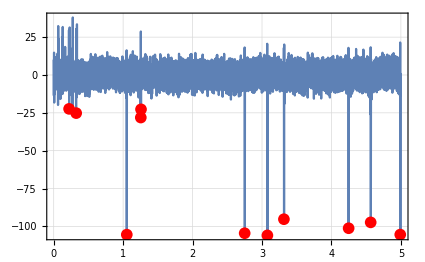

```mathematica
With[{m5=analogData["M5"]},
Show[ListLinePlot[TimeSeriesWindowResample[m5,{0,5,1000}]],ListPlot[{#,m5[#]}&/@spikeData["M5"],PlotStyle->Red]]]
```

Get a quick overview of spiking activity :

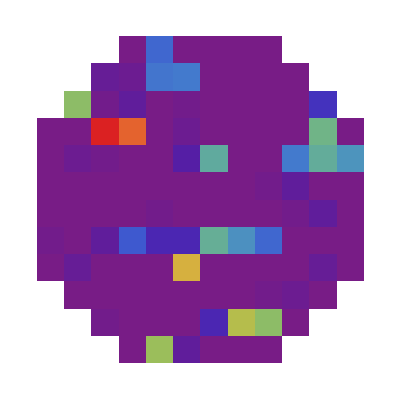

```mathematica
MEA120ActivityPlot[spikeData]
```

A histogram of inter-spike intervals for a given channel :

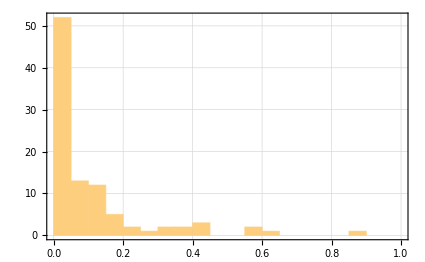

```mathematica
Histogram[Differences[spikeData["D4"]],{0,1,0.05}]
```

A CDF of inter-spike intervals for a given channel:

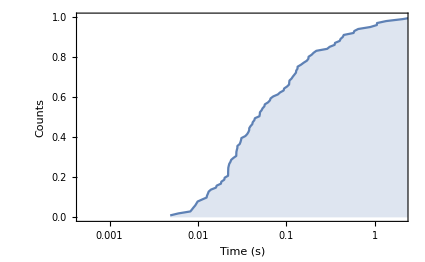

```mathematica
MEAIntervalLogCDFPlot[spikeData["D4"]]
```

Or for the whole array:

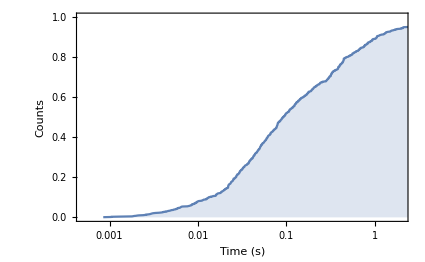

```mathematica
MEAIntervalLogCDFPlot[spikeData]
```

We can also export the CDF data to a csv file:

```mathematica
delayData=Sort[Differences[spikeData["D4"]]];
Export["cdf_data.csv",Transpose[{delayData,Range[Length[delayData]]}]]
```

cdf_data.csv

#### Raster Plots

Display an overview of the spiking activity of the whole array. Click on the plot, then press "." and it will display the electrode id:

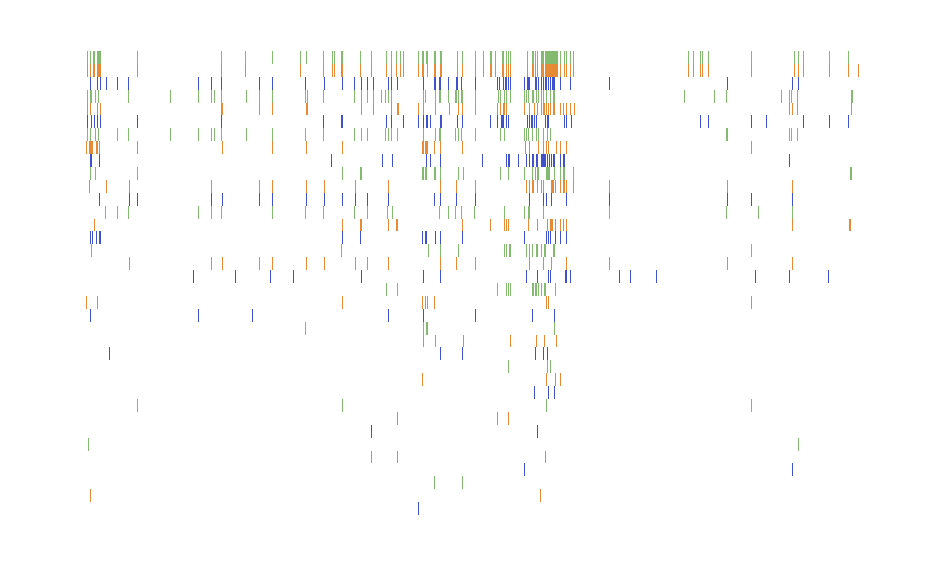

```mathematica
MEARasterPlot[spikeData]
```

or just a few channels:

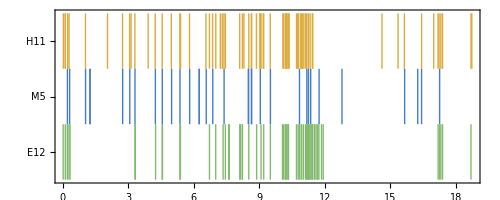

```mathematica
MEARasterPlot[KeyTake[spikeData,{"H11","M5","E12"}],ImageSize->500,PerformanceGoal->"Quality",AspectRatio->0.4]
```

It might be nice to have that be interactive:

```mathematica
MEARasterComparison[spikeData,{"H11","M5","E12"}]
```

#### Spike Delay Histograms

Show a histogram of the spike delay in M5 after each spike in H11 within 50 ms:

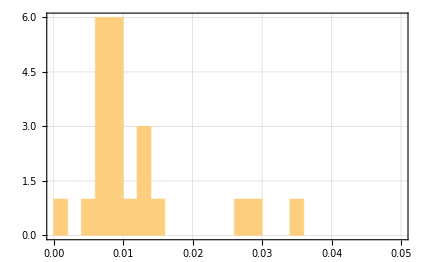

```mathematica
MEASpikeDelayHistogram[spikeData["H11"],spikeData["J8"],0.05]
```

Show the histogram for every channel for a given channel:

```mathematica
MEA120SpikeDelayHistogram[spikeData,"G8",0.05]
```

|  |  | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
 |  | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
 |  | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
 |  |  | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |

|  |  | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
 |  | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
 |  | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
 |  |  | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |

Perhaps we want to display a histogram of delays from a stimulus. The following example does that with stimulus times that start at 3.05 s, end at 150.05 s and occur every 2 s. Change “Count” to “CumulativeCount” for a cumulative distribution. 0.05 is the time window to look for a spike in. “A8” highlights A8 on the graph.

```mathematica
MEA120DelayHistogram[spikeData,"A8",{3.05,150.05,2},"Count",0.05]
```

|  |  | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  | 
 |  | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
 |  | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
 |  |  | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |

Show one plot from the grid above :

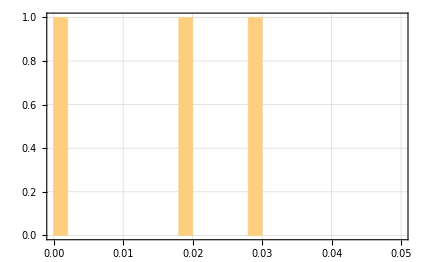

```mathematica
MEADelayHistogram[StimulusTimes[{3.05,150.05,2}],spikeData["D4"],0.05]
```

#### Network Graphs

Based on the above delay plots we would expect H8 to be a presynaptic connection to M5. Let’s see what other channels might have similar relationships. ProbableSynapticConnections finds the delay time for a spike in the target channel for every spike in the trigger channel. The subset of those delay times that are less than 15ms is taken. If that list contains more than 10 events, has a mean delay of greater than 1ms and a standard deviation of less than 2.5ms a trigger-target relationship is infered between the two electrodes under consideration:

```mathematica
synapticConnections=ProbableSynapticConnections[spikeData]
```

{C4->M5,D4->M5,F9->M5,F9->J8,J11->H11,L4->G8,L5->C4,L5->J8,M5->F9,M5->L4,M5->J8,H8->F9,H8->H11,H8->J11,H8->L5,H8->M5,H8->J8}

We can make a little interface to view the histogram and raster plot for each of these possible synaptic connections:

```mathematica
Manipulate[Column[{
MEASpikeDelayHistogram[spikeData[First@connection],spikeData[Last@connection],0.05],
MEARasterComparison[spikeData,{First@connection,Last@connection}]
}],
{connection,synapticConnections}]
```

We can also display an interactive network graph. Click on any electrode to see the electrodes that it drives:

```mathematica
MEA120InteractiveHighlightGraph[synapticConnections]
```

We can display the same graph in a way that shows its functional structure:

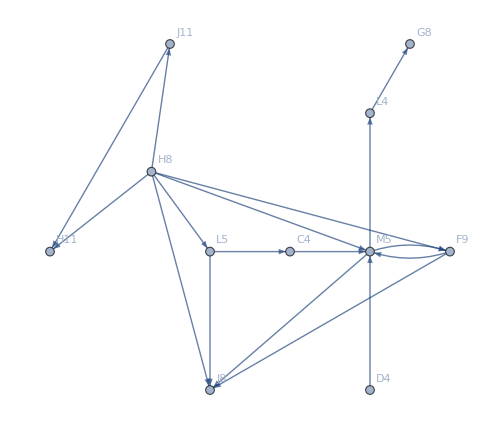

```mathematica
Graph[synapticConnections,VertexLabels->"Name",ImageSize->500,GraphLayout->"RadialDrawing"]
```

```mathematica
SynapticMeasure[trigger_,target_]:=Module[{filteredDelays},
filteredDelays=Select[MEASpikeDelays[trigger,target],#<0.015&];
If[Length@filteredDelays>10,Kurtosis[filteredDelays],0]
]
ProbableSynapticConnections[spikeData_]:=Module[{},
Parallelize[Apply[DirectedEdge,Select[Tuples[Keys[spikeData],2],
SynapticMeasure[spikeData[#[[1]]],spikeData[#[[2]]]]&],{1}]]
];
```

```mathematica
k=SynapticMeasure[spikeData[#[[1]]],spikeData[#[[2]]]]&/@Tuples[Keys@spikeData,2];
```

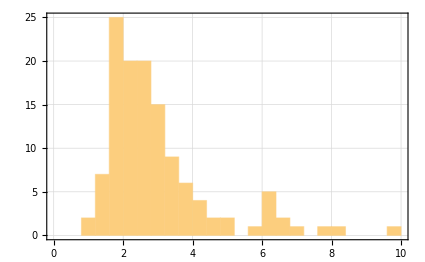

```mathematica
Histogram[DeleteCases[k,0],{0,10,0.4}]
```

```mathematica
Kurtosis@Select[MEASpikeDelays[spikeData["E12"],spikeData["L4"]],0<#<0.015&]
```

2.37433